```mathematica
5!
```

120

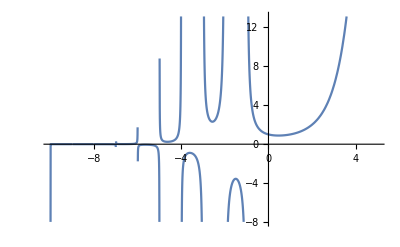

```mathematica
Plot[x!,{x,-10,5}]
```

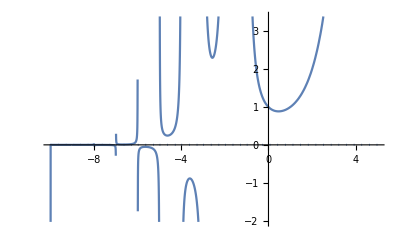

```mathematica
ReImPlot[x!,{x,-10,5}]
```

```mathematica
ⅈ!
```

ⅈ!

```mathematica
N[ⅈ!]
```

0.498016-0.15495 ⅈ

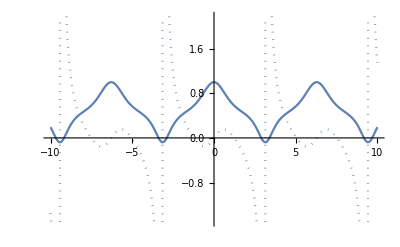

```mathematica
ReImPlot[(ⅇ^(ⅈ x))!,{x,-10,10}]
```

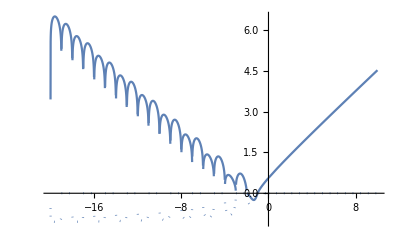

```mathematica
ReImPlot[(x!)^(1/x),{x,-20,10}]
```

```mathematica
f[x_]=(x!)^(1/x)
```

(x!)^(1/x)

```mathematica
D[x!,x]
```

Gamma[1+x] PolyGamma[0,1+x]

```mathematica
Limit[f'[x],x->∞]
```

1/ⅇ

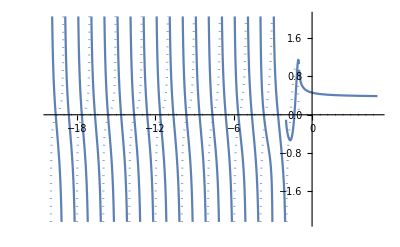

```mathematica
ReImPlot[f'[x],{x,-20,5}]
```

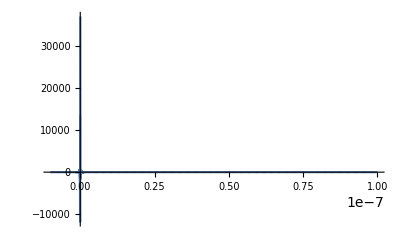

```mathematica
ReImPlot[f'[x],{x,-1 10^-8,1 10^-7},PlotRange->Full]
```

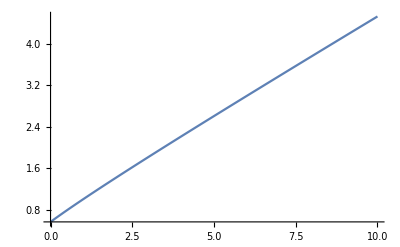

```mathematica
Plot[f[x],{x,0,10}]
```

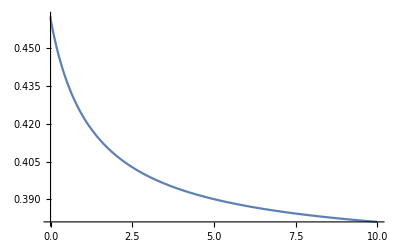

```mathematica
Plot[f'[x],{x,0,10 }]
```

```mathematica
Manipulate[
Plot[f'[x],{x,0,1 10^a}],
{a,-8,-1}
]
```

```mathematica
Limit[f'[x],x->0]
```

1/12 ⅇ^-EulerGamma π^2

```mathematica
%//N
```

0.461782

```mathematica
Series[f[x],{x,0,10}]
```

ⅇ^-EulerGamma+1/12 ⅇ^-EulerGamma π^2 x+9+O[x]^11
 |  |  |  |

```mathematica
Series[f[x],{x,Infinity,10}]
```

(ⅇ^((-1+Log[x]) x+O[1/x]^11) (√(2 π) √x+1/6 √(π/2) √(1/x)+1/144 √(π/2) (1/x)^(3/2)-(139 √(π/2) (1/x)^(5/2))/25920-(571 √(π/2) (1/x)^(7/2))/1244160+(163879 √(π/2) (1/x)^(9/2))/104509440+(5246819 √(π/2) (1/x)^(11/2))/37623398400-(534703531 √(π/2) (1/x)^(13/2))/451480780800-(4483131259 √(π/2) (1/x)^(15/2))/43342154956800+(432261921612371 √(π/2) (1/x)^(17/2))/257452400443392000+(6232523202521089 √(π/2) (1/x)^(19/2))/43252003274489856000+O[1/x]^(21/2)))^(1/x)

```mathematica
%//Normal//Simplify
```

2^(-55/2/x) 322252536375^(-1/x) π^(1/2/x) (ⅇ^-x x^(-19/2+x) (6232523202521089+72620002830878328 x-4473806345981280 x^2-51224769374929920 x^3+6031763270184960 x^4+67822533970329600 x^5-19850255489433600 x^6-231945542251315200 x^7+300361133850624000 x^8+7208667212414976000 x^9+86504006548979712000 x^10))^(1/x)

```mathematica
FindRoot[Cos[x]==x,{x,0}]
```

{x→0.739085}

```mathematica
π/2 Exp[Integrate[ArcTan[((π x+2)Log[(Sqrt[1-x^2]+1)/x]x)/(x^2 Log[(Sqrt[1-x^2]+1)/x]^2-π x-1)]/x,{x,0,1}]/π]//N
```

0.739085

```mathematica
Integrate[1/Log[x],x]
```

LogIntegral[x]

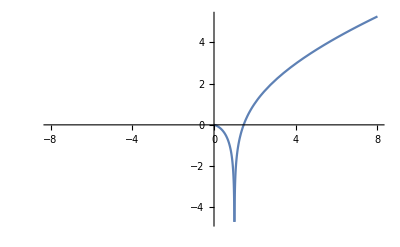

```mathematica
Plot[LogIntegral[x],{x,-8,8}]
```

General::munfl: Exp[-51179.] is too small to represent as a normalized machine number; precision may be lost.

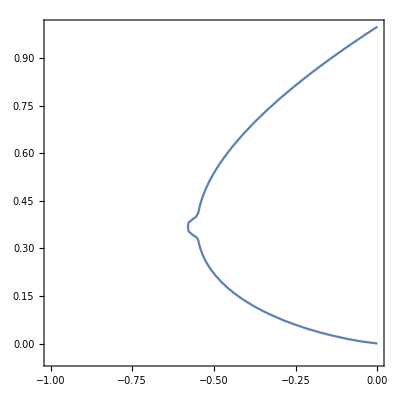

```mathematica
ContourPlot[x==1.5y Log[y]-1/36 Exp[-(36y-36/2.7183)^4],{x,-1,0},{y,-0.05,1}]
```